```mathematica
goodlcs=Join[refinement,refinement2]
```

{{1,{4.50358,0,1}},{1,{8.87438,0,1}},{1,{14.7308,0,1}},{1,{22.0729,1,2}},{1,{31.0131,1,2}},{1,{41.5944,1,2}},{1,{53.6183,1,2}},{1,{67.2833,1,2}},{1,{82.434,1,2}},{1,{99.1828,1,2}},{1,{117.53,1,2}},{1,{137.405,1,2}},{1,{158.879,1,2}},{1,{181.795,1,2}},{1,{206.395,1,2}},{1,{232.551,1,2}},{1,{260.235,1,2}},{1,{289.517,1,2}},{1,{320.441,1,2}},{1,{352.807,1,2}},{1,{386.814,1,2}},{1,{422.419,1,2}},{1,{459.51,1,2}},{1,{498.242,1,2}},{1,{538.416,1,2}},{1,{580.232,1,2}},{1,{623.646,1,2}},{1,{668.588,1,2}},{1,{715.086,1,2}},{1,{763.267,1,2}},{1,{813.004,1,2}},{1,{864.114,1,2}},{1,{916.977,1,2}},{1,{971.327,1,2}},{1,{4.53873,0,1}},{1,{8.86266,0,1}},{1,{14.7191,0,1}},{1,{22.1315,0,1}},{1,{31.0717,0,1}},{1,{41.5827,0,1}},{1,{53.63,0,1}},{1,{67.2716,0,1}},{1,{82.4457,0,1}},{1,{99.1945,0,1}},{1,{117.494,0,1}},{1,{137.37,0,1}},{1,{158.82,0,1}},{1,{181.83,0,1}},{1,{206.407,0,1}},{1,{232.539,0,1}},{1,{260.247,0,1}},{1,{289.529,0,1}},{1,{320.382,0,1}},{1,{352.795,0,1}},{1,{386.779,0,1}},{1,{422.313,0,1}},{1,{459.428,0,1}},{1,{498.113,0,1}},{1,{538.381,0,1}},{1,{580.197,0,1}},{1,{623.587,0,1}},{1,{668.553,0,1}},{1,{715.097,0,1}},{1,{763.185,0,1}},{1,{812.875,0,1}},{1,{864.102,0,1}},{1,{916.919,0,1}},{1,{971.291,0,1}}}

```mathematica
final=Table[{goodlcs[[i,2,1]],goodlcs[[i,2,1]]-goodlcs[[i+Length[goodlcs]/2,2,1]]},{i,1,Length[goodlcs]/2}]
```

{{4.50358,-0.0351563},{8.87438,0.0117188},{14.7308,0.0117188},{22.0729,-0.0585938},{31.0131,-0.0585938},{41.5944,0.0117188},{53.6183,-0.0117188},{67.2833,0.0117188},{82.434,-0.0117188},{99.1828,-0.0117188},{117.53,0.0351563},{137.405,0.0351563},{158.879,0.0585938},{181.795,-0.0351563},{206.395,-0.0117188},{232.551,0.0117188},{260.235,-0.0117188},{289.517,-0.0117188},{320.441,0.0585938},{352.807,0.0117188},{386.814,0.0351563},{422.419,0.105469},{459.51,0.0820313},{498.242,0.128906},{538.416,0.0351563},{580.232,0.0351563},{623.646,0.0585938},{668.588,0.0351563},{715.086,-0.0117188},{763.267,0.0820313},{813.004,0.128906},{864.114,0.0117188},{916.977,0.0585938},{971.327,0.0351563}}

## Weighted Fit

```mathematica
SetDirectory["~/Desktop/Ellen/Thesis/Calculations/Angular Momentum/"]
```

/Network/Servers/Knowlton.local/Users/zphantom/Desktop/Ellen/Thesis/Calculations/Angular Momentum

```mathematica
final=Import["l0.csv"]
```

{{0.842713,0.0020941},{3.2268,0.00229431},{7.17497,0.00269583},{12.6913,0.00346947},{19.7775,0.00475595},{28.4344,0.00669386},{38.6626,0.0094276},{50.4627,0.0131034},{63.8351,0.0178754},{78.7803,0.0239015},{95.2986,0.0313509},{113.39,0.0404018},{133.056,0.0512411},{154.296,0.0640718},{177.111,0.0791079},{201.501,0.0965832},{227.466,0.116748},{255.008,0.139874},{284.126,0.166259},{314.821,0.196228},{347.094,0.230135},{380.945,0.26837},{416.374,0.311363},{453.384,0.359593},{491.974,0.413585},{532.145,0.473925},{573.898,0.541265},{617.235,0.616334},{662.155,0.699948},{708.661,0.793022},{756.755,0.896585},{806.436,1.0118},{857.707,1.13997},{910.571,1.28259},{965.028,1.44135}}

This data is from parallelsperiment_mod -- I just copied over the “final” list. It was produced by refining the ranges and then bisecting, at rhoinf ~= 40λ and rhoinf ~= 80λ. It contains all the critical values of lambda between 0 and 1000.

```mathematica
loglog=Table[{Log[N[i]],Log[final[[i,1]]],1/final[[i,1]]*final[[i,2]]},{i,1,Length[final]}]
```

{{0.,-0.171128,0.00248495},{0.693147,1.17149,0.000711019},{1.09861,1.9706,0.000375728},{1.38629,2.54092,0.000273373},{1.60944,2.98454,0.000240473},{1.79176,3.3476,0.000235414},{1.94591,3.65487,0.000243843},{2.07944,3.92123,0.000259666},{2.19722,4.1563,0.000280025},{2.30259,4.36666,0.000303394},{2.3979,4.55702,0.000328975},{2.48491,4.73084,0.000356307},{2.56495,4.89077,0.000385109},{2.63906,5.03887,0.000415252},{2.70805,5.17678,0.000446657},{2.77259,5.30579,0.000479319},{2.83321,5.427,0.000513252},{2.89037,5.54129,0.000548509},{2.94444,5.64942,0.000585162},{2.99573,5.752,0.000623299},{3.04452,5.84959,0.000663034},{3.09104,5.94265,0.000704485},{3.13549,6.03159,0.000747796},{3.17805,6.11674,0.000793131},{3.21888,6.19843,0.000840665},{3.2581,6.27692,0.000890594},{3.29584,6.35245,0.000943138},{3.3322,6.42525,0.000998541},{3.3673,6.4955,0.00105708},{3.4012,6.56338,0.00111904},{3.43399,6.62904,0.00118478},{3.46574,6.69262,0.00125465},{3.49651,6.75426,0.00132909},{3.52636,6.81407,0.00140856},{3.55535,6.87216,0.00149358}}

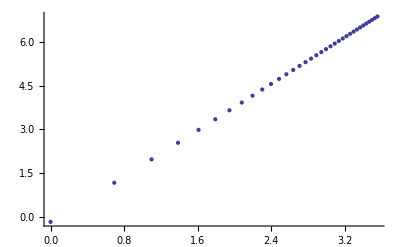

```mathematica
ListPlot[Table[{loglog[[i,1]],loglog[[i,2]]},{i,1,Length[loglog]}]]
```

Using w_i = 1/Δi^2, from Taylor.

```mathematica
weights=Table[1/(loglog[[i,3]]^2),{i,1,Length[loglog]}];
```

This is also from Taylor, used below

```mathematica
Delta=Sum[weights[[i]],{i,Length[weights]}]*Sum[weights[[i]]*loglog[[i,1]]^2,{i,Length[loglog]}]-(Sum[weights[[i]]*loglog[[i,1]],{i,Length[loglog]}])^2;
```

More symbols to make expressions less unweildy.

```mathematica
x[i_]:=loglog[[i,1]];
y[i_]:=loglog[[i,2]];
w[i_]:=weights[[i]];
```

Now, the fit coefficients (for line off form y = A + Bx):

```mathematica
A=1/Delta(Sum[w[i]*x[i]^2,{i,Length[loglog]}]*Sum[w[i]*y[i],{i,Length[loglog]}]-Sum[w[i]*x[i],{i,Length[loglog]}]*Sum[w[i]*x[i]*y[i],{i,Length[loglog]}])
```

-0.224553

```mathematica
B=1/Delta(Sum[w[i],{i,Length[loglog]}]*Sum[w[i]*x[i]*y[i],{i,Length[loglog]}]-Sum[w[i]*x[i],{i,Length[loglog]}]*Sum[w[i]*y[i],{i,Length[loglog]}])
```

1.99448

Again, not quite quadratic. We can plot both:

```mathematica
F[x_]:=A+B*x
```

```mathematica
Needs["ErrorBarPlots`"]
```

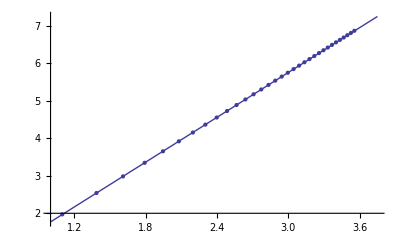

```mathematica
Show[Plot[F[x],{x,1.,3.75}],ErrorListPlot[Table[{{x[i],y[i]},ErrorBar[loglog[[i,3]]]},{i,1,Length[loglog]}]]]
```

Uncertainties in A and B:

```mathematica
Inverse[{{a,b},{b,c}}]
```

{{c/(-b^2+a c),-b/(-b^2+a c)},{-b/(-b^2+a c),a/(-b^2+a c)}}

```mathematica
%100//MatrixForm
```

(c/(-b^2+a c) | -b/(-b^2+a c)
-b/(-b^2+a c) | a/(-b^2+a c))

```mathematica
σA=Sqrt[Sum[w[i]*x[i]^2,{i,Length[loglog]}]/Delta]
```

0.000282004

```mathematica
σB=Sqrt[Sum[w[i],{i,Length[loglog]}]/Delta]
```

0.000124848

```mathematica
B+σB
```

1.9946

This is the max value for B:

```mathematica
B+%22
```

{2.07695,1.87963}

Checking the goodness of the fit:

```mathematica
fitvals=Table[F[loglog[[i,1]]],{i,1,Length[loglog]}];
```

```mathematica
residuals=Table[fitvals[[i]]-loglog[[i,2]],{i,1,Length[loglog]}];
```

These look like a curve, not random, which kind of worries me a bit. That said, the fit looks okay.

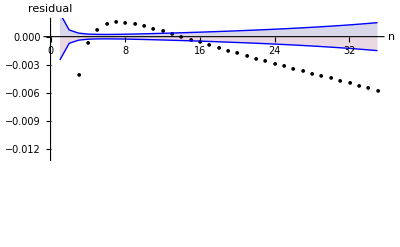

```mathematica
Show[ListPlot[residuals,PlotStyle->Black,PlotMarkers->{Automatic,5},AxesLabel->{"n","residual"}],ListPlot[{Table[loglog[[i,3]],{i,1,Length[loglog]}],Table[-loglog[[i,3]],{i,1,Length[loglog]}]},PlotStyle->Blue,Joined->True,Filling->Axis]]
```

```mathematica
?PlotStyle
```

PlotStyle is an option for plotting and related functions that specifies styles in which objects are to be drawn.

This expression should output a list of booleans. TRUE means that the fit is inside the error bars (resdiual < error bar) and FALSE means it’s outside

```mathematica
Table[Abs[residuals[[i]]]<loglog[[i,3]],{i,1,Length[loglog]}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

Making sure nothing stupid happened:

```mathematica
fitvals
```

{-0.224553,1.15791,1.96661,2.54038,2.98544,3.34907,3.65652,3.92285,4.15776,4.3679,4.558,4.73154,4.89118,5.03899,5.17659,5.30531,5.42623,5.54023,5.64807,5.75037,5.84768,5.94046,6.02912,6.11401,6.19542,6.27365,6.34892,6.42146,6.49145,6.55906,6.62446,6.68778,6.74916,6.8087,6.86651}

```mathematica
Table[loglog[[i,2]],{i,1,Length[loglog]}]
```

{-0.171128,1.17149,1.9706,2.54092,2.98454,3.3476,3.65487,3.92123,4.1563,4.36666,4.55702,4.73084,4.89077,5.03887,5.17678,5.30579,5.427,5.54129,5.64942,5.752,5.84959,5.94265,6.03159,6.11674,6.19843,6.27692,6.35245,6.42525,6.4955,6.56338,6.62904,6.69262,6.75426,6.81407,6.87216}

Not...that I can see :( :( :(

## General Quadratic Fit

```mathematica
quadfit=FindFit[Table[final[[i,1]],{i,1,Length[final]}],a x^2 + b x + c, {a,b,c},{x}]
```

{a→0.788643,b→-0.044004,c→0.268191}

```mathematica
G[x_]:=c x^2 + b x + a /.ftest
```

```mathematica
quadfitvals=Table[G[i],{i,1,Length[final]}];
```

```mathematica
quadresiduals=Table[quadfitvals[[i]]-final[[i,1]],{i,1,Length[final]}];
```

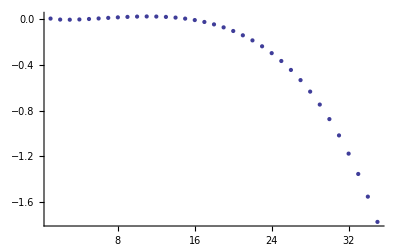

```mathematica
ListPlot[quadresiduals]
```

```mathematica
Table[Abs[quadresiduals[[i]]]<final[[i,2]],{i,1,Length[final]}]
```

{False,False,False,True,True,True,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False}

```mathematica
Count[%91,False]
```

14

```mathematica
Count[%91,True]
```

21

```mathematica
21/35//N
```

0.6

```mathematica
Table[Abs[qres[[i]]]<final[[i,2]],{i,1,Length[final]}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Count[%95,False]
```

14

```mathematica
Count[%95,True]
```

21

```mathematica
H[x_]:=c x^2 + b x + a /.ftest2
```

```mathematica
qfvs=Table[H[i],{i,1,Length[final]}];
```

```mathematica
qres=Table[qfvs[[i]]-final[[i,1]],{i,1,Length[final]}];
```

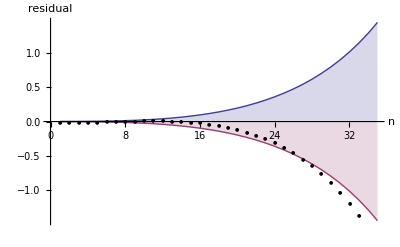

```mathematica
Show[
ListPlot[{Table[final[[i,2]],{i,1,Length[final]}],Table[-final[[i,2]],{i,1,Length[final]}]},Joined->True,Filling->Axis,AxesLabel->{"n","residual"}],
ListPlot[quadresiduals,PlotStyle->Black,PlotMarkers->{Automatic,5}]
]
```

```mathematica
Table[Abs[qres[[i]]]<final[[i,2]],{i,1,Length[final]}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}